# 1. Interface

# Séance M 1 (Title)

## One-liners (Subtitle)

Introduction à l’organisation de l’interface
Nom Prénom : xxxdi xx mois année (Subsubtitle)

## 1. Mise en Forme Générale (section)

### A. L’interface (sous-section)

#### 1. sous-sous-section n°1

texte
texte : la cellule ci dessous est une cellule d”Input”

```mathematica
3+5
```

8

#### 2. sous-sous-section n°2

texte
texte : la cellule ci-dessous est une autre cellule d”Input”

```mathematica
4+6
```

10

### B. Le noyau (sous-section)

#### 1. sous-sous-section

texte

## II. Mise en Forme spécifique

### 1. Saisie

#### I. Avec la palette Texte (Writing Assistant)

Dans une cellule “Texte” saisir les formules :
∑_(i=1)^10 i,	∑_(i=1)^n i,	(1 | 2
3 | 4)
(NB: utiliser Tab pour passer d’une case à l’autre)

# II. Un tour introductif

## A. Opérations de base (symboliques avec précision arbitraire)

```mathematica
Bonjour ! (* Interpreter comme un string *)
```

Bonjour!

```mathematica
Cos[Pi](* Mathematica connait les regles de trigonometrie donc il recalcule ! *)
```

-1

```mathematica
N[Pi,10] (* Approximation avec notre de décimal voulue *)
```

3.141592654

```mathematica
{Cos[x], x^2, x+2} /. x-> Pi (* Résultats de plusieurs fonctions en une ligne *)
```

{-1,π^2,2+π}

```mathematica
3x+2x (* Reconnaissance des variables et traitement du calcul algébrique automatique *)
```

5 x

```mathematica
3^100 (* Puissance classique *)
```

515377520732011331036461129765621272702107522001

```mathematica
True || False (* Logique booléenne implementée *)
```

False

```mathematica
True && !False
```

True

```mathematica
3^10; //AbsoluteTiming
```

{2.7×10^-6,Null}

```mathematica
3^100; //AbsoluteTiming
```

{0.0000258,Null}

```mathematica
3^1000; //AbsoluteTiming
```

{0.0000292,Null}

```mathematica
3^10000; //AbsoluteTiming
```

{0.0005636,Null}

```mathematica
3^100000; //AbsoluteTiming
```

{0.0007345,Null}

```mathematica
3^1000000;//AbsoluteTiming (* Calcul très rapide peu importe la puissance car mathematica sait simplifier les calculs avec puissance *)
```

{0.0042005,Null}

## B. Opérations de base (numériques)

```mathematica
(10.2 - 3.1)*6.2/2.9  (* Connaissance des priorités de calculs et des règles de bases *)
```

```mathematica
15.17930344827588
```

```mathematica
(2+3I)*(4-5I)  (* Connaissance du monde des complexes *)
```

23+2 ⅈ

## C. Nombres et Fonctions élémentaires

```mathematica
N[Pi]
```

3.14159

```mathematica
e
```

e

```mathematica
N[E] (* Approximation de e *)
```

2.71828

```mathematica
N[Infinity] (* Valeurs infinies implémentées *)
```

∞

```mathematica
N[I]
```

0.+1. ⅈ

```mathematica
{E^x, Sqrt[x], Ln[x], Log[x], Abs[x], Factorial[x]} /. x-> 1 (* Fonction racine, ln, log etc... implementées *)
```

{ⅇ,1,Ln[1],0,1,1}

## D. Fonctions

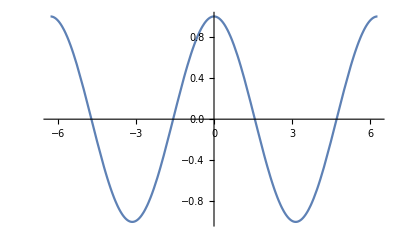

```mathematica
Plot[ (* Possibilité de tracer des courbes et d'ajuster les fênetres avec Plot... *)
Cos[x],
{x, -2Pi, 2Pi}
]
```

```mathematica
Manipulate[ (* ...mais aussi des variables de la fonction avec Manipulate *)
Plot[
Cos[a*x+b],
{x, -2Pi,2Pi}
],
{a, 1, 10},
{b, 0, 2Pi}
]
```

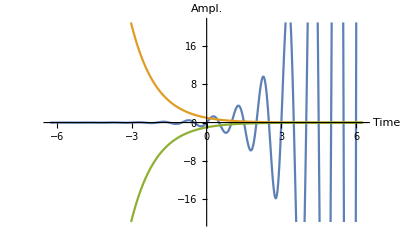

```mathematica
Plot[ (* Possibilité de tracer plusieurs courbes sur le même Plot, de changer les couleurs, de comparer etc... *)
{E^x*Sin[2Pi*x], Exp[-x], -Exp[-x]}, (* Fonctions tracées *)
{x, -2Pi, 2Pi}, (* Fenêtre *)
AxesLabel->{"Time", "Ampl."} (* Ajout de titres pour les axes *)
]
```

```mathematica
h[x_] = (a*x^4)/(b+x^3) (* Implémentation de fonctions *)
```

(a x^4)/(b+x^3)

```mathematica
Manipulate[Plot[a*x^4/(b+x^3),{x,-8,8}],{a,-8,8},{b,-2,2}] (* Tracable et manipulable *)
```

```mathematica
ResourceFunction["InflectionPoints"][(a*x^4)/(b+x^3),x] (* Possibilité d'utiliser les fonctions de mathematica afin d'automatiquement calculer des points d'inflexions *)
```

[(a x^4)/(b+x^3),x]

```mathematica
∂_x ((a*x^4)/(b+x^3)) (* mais aussi des dérivées *)
```

-(3 a x^6)/((b+x^3)^2)+(4 a x^3)/(b+x^3)

```mathematica
h'[x]  (* autre notation possibile *)
```

-(3 a x^6)/((b+x^3)^2)+(4 a x^3)/(b+x^3)

```mathematica
∂_x ∂_x ∂_x ∂_x ∂_x (a*x^4)/(b+x^3) (* ou des dérivées 5eme *)
```

-(29160 a x^14)/((b+x^3)^6)+(77760 a x^11)/((b+x^3)^5)-(71280 a x^8)/((b+x^3)^4)+(25200 a x^5)/((b+x^3)^3)-(2520 a x^2)/((b+x^3)^2)

```mathematica
Solve[h[s] == a/2, s] (* Possibilité de résoudre des équations *)
```

{{s→1/8-1/8 √(1-(64 (2/3)^(1/3) b)/((-9 b+√3 √(27 b^2+2048 b^3))^(1/3))+4 (2/3)^(2/3) (-9 b+√3 √(27 b^2+2048 b^3))^(1/3))-1/2 √(1/8+(4 (2/3)^(1/3) b)/((-9 b+√3 √(27 b^2+2048 b^3))^(1/3))-((-9 b+√3 √(27 b^2+2048 b^3))^(1/3))/(2 2^(1/3) 3^(2/3))-1/(8 √(1-(64 (2/3)^(1/3) b)/((-9 b+√3 √(27 b^2+2048 b^3))^(1/3))+4 (2/3)^(2/3) (-9 b+√3 √(27 b^2+2048 b^3))^(1/3))))},{s→1/8-1/8 √(1-(64 (2/3)^(1/3) b)/((-9 b+√3 √(27 b^2+2048 b^3))^(1/3))+4 (2/3)^(2/3) (-9 b+√3 √(27 b^2+2048 b^3))^(1/3))+1/2 √(1/8+(4 (2/3)^(1/3) b)/((-9 b+√3 √(27 b^2+2048 b^3))^(1/3))-((-9 b+√3 √(27 b^2+2048 b^3))^(1/3))/(2 2^(1/3) 3^(2/3))-1/(8 √(1-(64 (2/3)^(1/3) b)/((-9 b+√3 √(27 b^2+2048 b^3))^(1/3))+4 (2/3)^(2/3) (-9 b+√3 √(27 b^2+2048 b^3))^(1/3))))},{s→1/8+1/8 √(1-(64 (2/3)^(1/3) b)/((-9 b+√3 √(27 b^2+2048 b^3))^(1/3))+4 (2/3)^(2/3) (-9 b+√3 √(27 b^2+2048 b^3))^(1/3))-1/2 √(1/8+(4 (2/3)^(1/3) b)/((-9 b+√3 √(27 b^2+2048 b^3))^(1/3))-((-9 b+√3 √(27 b^2+2048 b^3))^(1/3))/(2 2^(1/3) 3^(2/3))+1/(8 √(1-(64 (2/3)^(1/3) b)/((-9 b+√3 √(27 b^2+2048 b^3))^(1/3))+4 (2/3)^(2/3) (-9 b+√3 √(27 b^2+2048 b^3))^(1/3))))},{s→1/8+1/8 √(1-(64 (2/3)^(1/3) b)/((-9 b+√3 √(27 b^2+2048 b^3))^(1/3))+4 (2/3)^(2/3) (-9 b+√3 √(27 b^2+2048 b^3))^(1/3))+1/2 √(1/8+(4 (2/3)^(1/3) b)/((-9 b+√3 √(27 b^2+2048 b^3))^(1/3))-((-9 b+√3 √(27 b^2+2048 b^3))^(1/3))/(2 2^(1/3) 3^(2/3))+1/(8 √(1-(64 (2/3)^(1/3) b)/((-9 b+√3 √(27 b^2+2048 b^3))^(1/3))+4 (2/3)^(2/3) (-9 b+√3 √(27 b^2+2048 b^3))^(1/3))))}}

## E. Graphiques 2D, 3D, sons et animations

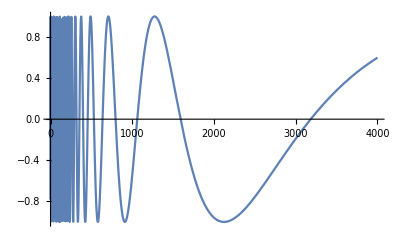

```mathematica
Plot[Sin[10000/t],{t,0,4000}] (* fonction tracée de 0 a 40000 *)
```

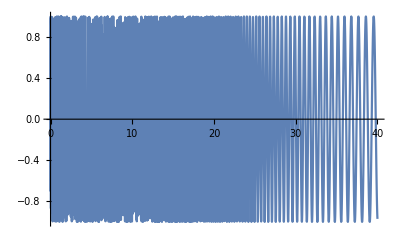

```mathematica
Plot[Sin[10000/t],{t,0,40}] (* Les bornes ne sont pas pratique pour observer la courbe, d'ou l'importance de choisir les bonnes bornes *)
```

```mathematica
Play[Sin[10000/t],{t,-2,-0.001}] (* Possibilité de jouer des sons, d'afficher des images etc... *)
```

-Graphics-

```mathematica
Plot3D[3x + 2y, (* Ou encore de tracer des courbes en 3D *)
{x,-10,10},{y,-10,10}
]
```

-Graphics3D-

```mathematica
Manipulate[  (* qui sont aussi manipulables ! *)
Plot3D[
3*x*a + 2*y*b,
{x,-10,10},{y,-10,10}
]
,{a,-10,10},{b,-10,10}
]
```